## Asymptotic expansion of error

```mathematica
f[dy_]:=(1 - Exp[-2n dx dy])PDF[NormalDistribution[0,1/(√n)],dg + dy -dx]
```

kth derivative at boundary

```mathematica
fd[k_]:=Evaluate[D[f[dy],{dy,k}]]/.dy-> 0//Simplify
```

```mathematica
Table[fd[k],{k,1,4}]
```

{dx ⅇ^(-1/2 (dg-dx)^2 n) n^(3/2) √(2/π),-2 dg dx ⅇ^(-1/2 (dg-dx)^2 n) n^(5/2) √(2/π),dx ⅇ^(-1/2 (dg-dx)^2 n) n^(5/2) (-3+3 dg^2 n+dx^2 n) √(2/π),-4 dg dx ⅇ^(-1/2 (dg-dx)^2 n) n^(7/2) (-3+dg^2 n+dx^2 n) √(2/π)}

Closed form expression in terms of Hermite polynomials (physcists)

```mathematica
Table[HermiteH[k,x],{k,3}]
```

{2 x,-2+4 x^2,-12 x+8 x^3}

```mathematica
Evaluate[D[(1 - Exp[-2n dx dy]),{dy,1}]]/. dy->0
```

2 dx n

```mathematica
pderiv1[k_]:=Evaluate[D[(1 - Exp[-2n dx dy]),{dy,k}]]/. dy->0
```

```mathematica
pderiv[k_]:= (-1)^(k+1)(2n dx)^k
```

```mathematica
Table[pderiv1[k],{k,0,4}]
```

{0,2 dx n,-4 dx^2 n^2,8 dx^3 n^3,-16 dx^4 n^4}

Note that the 0th derivative is wrong!

```mathematica
Table[pderiv[k],{k,0,4}]
```

{-1,2 dx n,-4 dx^2 n^2,8 dx^3 n^3,-16 dx^4 n^4}

```mathematica
Evaluate[D[PDF[NormalDistribution[0,1/(√n)],dg + dy -dx],{dy,2}]]/.dy-> 0//FullSimplify
```

(ⅇ^(-1/2 (dg-dx)^2 n) n^(3/2) (-1+(dg-dx)^2 n))/(√(2 π))

```mathematica
hderiv1[k_]:=Evaluate[D[PDF[NormalDistribution[0,1/(√n)],dg + dy -dx],{dy,k}]]/.dy-> 0//FullSimplify
```

```mathematica
hderiv[k_]:=(-1)^k(n/2)^(k/2)HermiteH[k,√(n/2)(dg + dy-dx)]PDF[NormalDistribution[0,1/(√n)],dg+dy-dx]/.dy-> 0//FullSimplify
```

```mathematica
Table[hderiv[k],{k,0,4}]
```

{(ⅇ^(-1/2 (dg-dx)^2 n) √n)/(√(2 π)),((-dg+dx) ⅇ^(-1/2 (dg-dx)^2 n) n^(3/2))/(√(2 π)),(ⅇ^(-1/2 (dg-dx)^2 n) n^(3/2) (-1+(dg-dx)^2 n))/(√(2 π)),((dg-dx) ⅇ^(-1/2 (dg-dx)^2 n) n^(5/2) (3-(dg-dx)^2 n))/(√(2 π)),(ⅇ^(-1/2 (dg-dx)^2 n) n^(5/2) (3+(dg-dx)^2 n (-6+(dg-dx)^2 n)))/(√(2 π))}

```mathematica
Table[hderiv1[k],{k,0,4}]
```

{(ⅇ^(-1/2 (dg-dx)^2 n) √n)/(√(2 π)),((-dg+dx) ⅇ^(-1/2 (dg-dx)^2 n) n^(3/2))/(√(2 π)),(ⅇ^(-1/2 (dg-dx)^2 n) n^(3/2) (-1+(dg-dx)^2 n))/(√(2 π)),((dg-dx) ⅇ^(-1/2 (dg-dx)^2 n) n^(5/2) (3-(dg-dx)^2 n))/(√(2 π)),(ⅇ^(-1/2 (dg-dx)^2 n) n^(5/2) (3+(dg-dx)^2 n (-6+(dg-dx)^2 n)))/(√(2 π))}

```mathematica
fdf[m_]:=∑_(k=1)^m Binomial[m,k]pderiv[k]hderiv[m-k]//FullSimplify
```

```mathematica
Table[Binomial[3,k]pderiv[k]hderiv[3-k],{k,1,3}]
```

{3 dx ⅇ^(-1/2 (dg-dx)^2 n) n^(5/2) (-1+(dg-dx)^2 n) √(2/π),-6 dx^2 (-dg+dx) ⅇ^(-1/2 (dg-dx)^2 n) n^(7/2) √(2/π),4 dx^3 ⅇ^(-1/2 (dg-dx)^2 n) n^(7/2) √(2/π)}

```mathematica
Table[Binomial[5,k]pderiv[k]hderiv[5-k],{k,1,5}]
```

{5 dx ⅇ^(-1/2 (dg-dx)^2 n) n^(7/2) (3+(dg-dx)^2 n (-6+(dg-dx)^2 n)) √(2/π),-20 (dg-dx) dx^2 ⅇ^(-1/2 (dg-dx)^2 n) n^(9/2) (3-(dg-dx)^2 n) √(2/π),40 dx^3 ⅇ^(-1/2 (dg-dx)^2 n) n^(9/2) (-1+(dg-dx)^2 n) √(2/π),-40 dx^4 (-dg+dx) ⅇ^(-1/2 (dg-dx)^2 n) n^(11/2) √(2/π),16 dx^5 ⅇ^(-1/2 (dg-dx)^2 n) n^(11/2) √(2/π)}

```mathematica
fdf1[m_]:=∑_(k=0)^m Binomial[m,k]pderiv1[m-k]hderiv1[k]//FullSimplify
```

```mathematica
Table[fdf1[m]/√n,{m,1,3,2}]
```

{dx ⅇ^(-1/2 (dg-dx)^2 n) n √(2/π),dx ⅇ^(-1/2 (dg-dx)^2 n) n^2 (-3+3 dg^2 n+dx^2 n) √(2/π)}

```mathematica
∫_0^∞ dx ⅇ^(-1/2 (dg-dx)^2 n) n^2 ⅆdx
```

ConditionalExpression[n^2 ((ⅇ^(-(dg^2 n)/2))/n+(dg √(π/2) (1+Erf[(dg √n)/(√2)]))/(√n)),(Re[n]≥0&&Re[dg n]<0)||Re[n]>0]

```mathematica
∫_0^∞ dx ⅇ^(-1/2 (dg-dx)^2 n) n^2 ⅆdx
```

ConditionalExpression[n^2 ((ⅇ^(-(dg^2 n)/2))/n+(dg √(π/2) (1+Erf[(dg √n)/(√2)]))/(√n)),(Re[n]≥0&&Re[dg n]<0)||Re[n]>0]

```mathematica
Table[fd[m],{m,1,4,2}]//FullSimplify
```

{fd[1],fd[3]}

```mathematica
pderiv[k]hderiv[m-k]//FullSimplify
```

((-1)^(1+m) 2^(1/2 (-1+3 k-m)) ⅇ^(-1/2 (dg-dx)^2 n) n^(1/2 (1-k+m)) (dx n)^k HermiteH[-k+m,((dg-dx) √n)/(√2)])/(√π)

```mathematica
Integrate[Cos[-2 π k x/h],x]
```

(h Sin[(2 k π x)/h])/(2 k π)

```mathematica
Integrate[(h Sin[(2 k π x)/h])/(2 k π),x]
```

-(h^2 Cos[(2 k π x)/h])/(4 k^2 π^2)

```mathematica
Integrate[-(h^2 Cos[(2 k π x)/h])/(4 k^2 π^2),x]
```

-(h^3 Sin[(2 k π x)/h])/(8 k^3 π^3)

```mathematica
Integrate[-(h^3 Sin[(2 k π x)/h])/(8 k^3 π^3),x]
```

(h^4 Cos[(2 k π x)/h])/(16 k^4 π^4)

```mathematica
test[h_]:=∑_(k=1)^∞ ∑_(m=1)^∞ (-1)^m(h/(2 π k))^(2m)(Cos[2 π k/h])
```

```mathematica
test2[h_]:=∑_(k=1)^∞ ∑_(m=1)^∞ (h/(2 π k))^(2m)
```

```mathematica
test2[1]//N
```

0.0423781

```mathematica
test2[0.7]//N
```

0.0205854

```mathematica
a = Table[test2[1/n]//N,{n,1,10,1}]
```

{0.0423781,0.0104603,0.00463823,0.00260688,0.00166778,0.00115794,0.00085063,0.000651211,0.000514509,0.000416736}

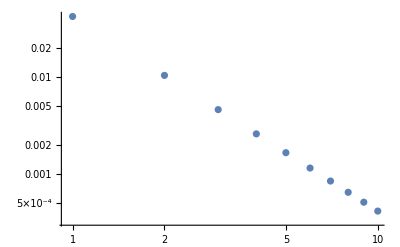

```mathematica
ListLogLogPlot[a]
```

h=1, test =0.04

```mathematica
test[0.3]//N
```

$Aborted

```mathematica
∑_(k=1)^∞ ∑_(m=1)^∞ (-1)^m(1/(2 π k))^m(Cos[2 π k])//N
```

$Aborted

```mathematica
Cos[2π 2 ]
```

1

```mathematica
∑_(k=1)^∞ ∑_(m=1)^∞ (-1)^m(1/(2 π k))^m//N
```

-30496.1+1.26969×10^-20 ⅈ

```mathematica
∑_(m=1)^∞ ∑_(k=1)^∞ (-1/(2 π k))^m//N
```

-30496.1

```mathematica
∑_(m=1)^∞ ∑_(k=1)^∞ (-1/k)^m//N
```

-191612.

```mathematica
Manipulate[LogPlot[{HermiteH[n,x],2^n x^n},{x,0,4}],{n,2,10}]
```

```mathematica
2^9
```

512

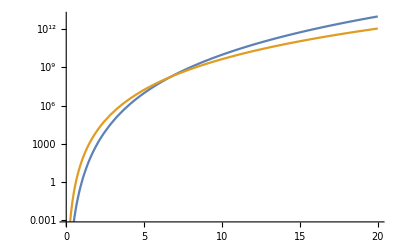

```mathematica
LogPlot[{x^10,45 x^8},{x,0,20}]
```

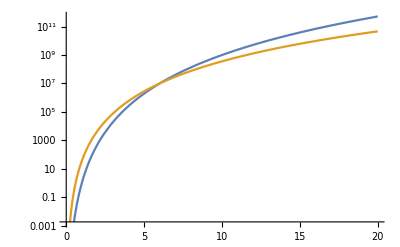

```mathematica
LogPlot[{x^9,36 x^7},{x,0,20}]
```

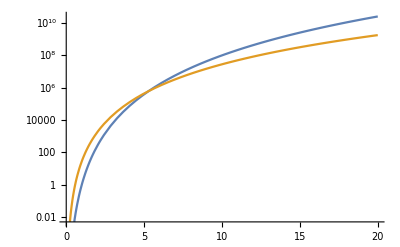

```mathematica
LogPlot[{x^8,28 x^6},{x,0,20}]
```

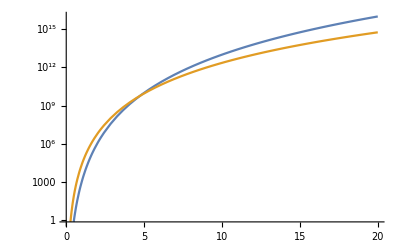

```mathematica
LogPlot[{1024 x^10,23040 x^8},{x,0,20}]
```

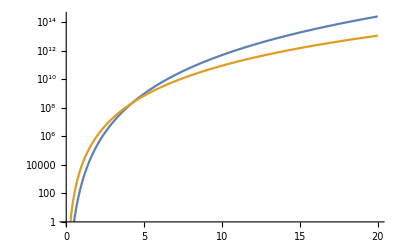

```mathematica
LogPlot[{512 x^9,9216 x^7},{x,0,20}]
```

```mathematica
∑_(k=1)^∞ ∑_(m=1)^∞ 1/(2π k)^(2m)//N
```

0.0423781

```mathematica
Table[∑_(k=1)^∞ 2/(2π k)^(2m),{m,1,10}]//N
```

{0.0833333,0.00138889,0.0000330688,8.2672×10^-7,2.08768×10^-8,5.28419×10^-10,1.33825×10^-11,3.38968×10^-13,8.58606×10^-15,2.17487×10^-16}

```mathematica
Table[BernoulliB[m],{m,1,10}]
```

{-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66}

```mathematica
∑_(k=1)^∞ BernoulliB[2k]/((2k)!)//N
```

0.0819767

```mathematica
Binomial[]
```

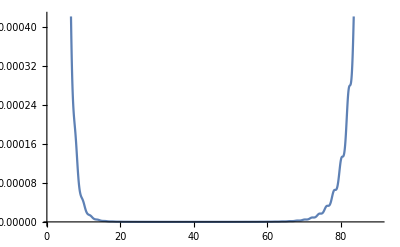

```mathematica
Plot[1/(2π)^m m!!,{m,1,90}]
```

```mathematica
D[f[dy],{dy,2}]//Simplify
```

1/(√(2 π))ⅇ^(-1/2 (4 dx dy+(dg-dx+dy)^2) n) n^(3/2) (1-dg^2 n-dx^2 n-2 dx dy n-dy^2 n-2 dg (dx+dy) n+ⅇ^(2 dx dy n) (-1+dg^2 n+dx^2 n-2 dx dy n+dy^2 n+2 dg (-dx+dy) n))

```mathematica
∫_0^∞ 1/(√(2 π))√n (-4 dx^2 ⅇ^(-2 dx dy n-1/2 (dg-dx+dy)^2 n) n^2)ⅆdy
```

ConditionalExpression[-2 dx^2 ⅇ^(2 dg dx n) n^2 Erfc[((dg+dx) √n)/(√2)],(Re[n]≥0&&Re[(dg+dx) n]>0)||Re[n]>0]